```mathematica
a = Import["C:\\Users\\Amit\\Dropbox\\Keystroke Timing\\KeystrokeTiming\\sounds\\a.mp3","Data"];
```

```mathematica
s = Import["C:\\Users\\Amit\\Dropbox\\Keystroke Timing\\KeystrokeTiming\\sounds\\s.mp3","Data"];
```

```mathematica
ListPlay[a[[150000;;300000]],SampleRate->44100]
```

-Graphics-

```mathematica
ListPlay[s[[150000;;300000]],SampleRate->44100]
```

-Graphics-

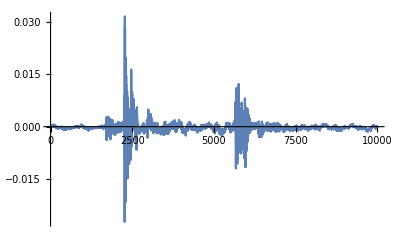

```mathematica
ListLinePlot[keys = s[[173000;;183000]],PlotRange->All]
```

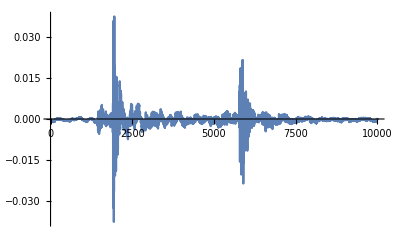

```mathematica
ListLinePlot[keya = a[[170000;;180000]],PlotRange->All]
```

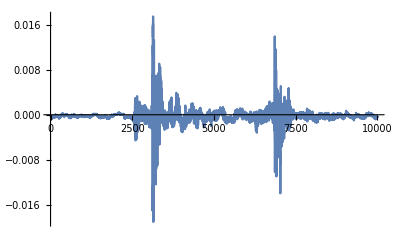

```mathematica
ListLinePlot[keya2 = a[[250000;;260000]],PlotRange->All]
```

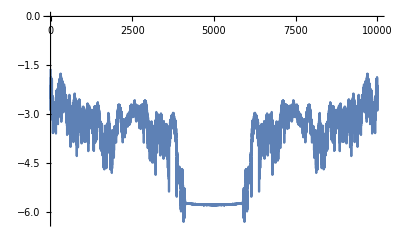

```mathematica
ListLinePlot[stuffs = Log10@Abs@Fourier[keys],PlotRange->All]
```

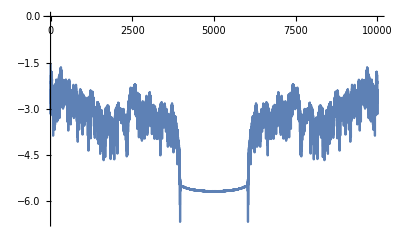

```mathematica
ListLinePlot[stuffa= Log10@Abs@Fourier[keya],PlotRange->All]
```

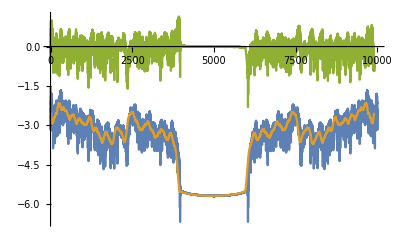

```mathematica
ListLinePlot[{stuffa,ma = MovingAverage[stuffa,100],siga = stuffa[[1;;Length[ma]]]-ma}]
```

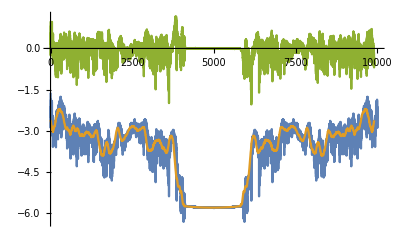

```mathematica
ListLinePlot[{stuffs,ms = MovingAverage[stuffs,100],sigs = stuffs[[1;;Length[ms]]]-ms}]
```

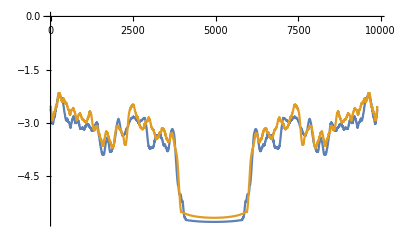

```mathematica
ListLinePlot[{ms,ma}]
```

```mathematica
specsig[data_]:= MovingAverage[Log10@Abs@Fourier[data],100];
```

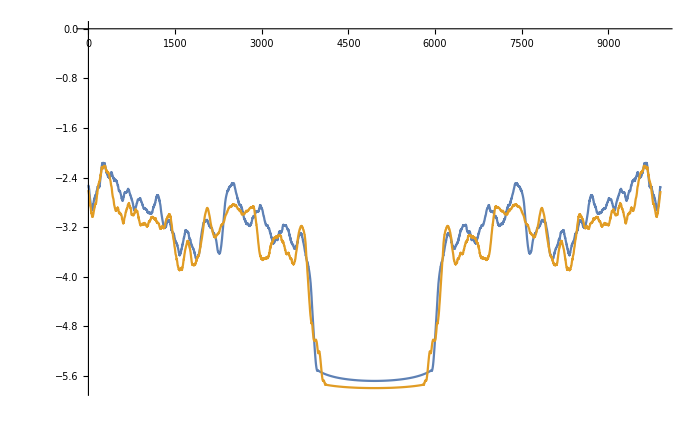

```mathematica
ListLinePlot[{specsig[keya],specsig[keys]}]
```

```mathematica
lsq[sig1_,ref_] := Total[(sig1 - ref)^2];
```

```mathematica
lsq[specsig[keys],specsig[keya]]
```

614.672